Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

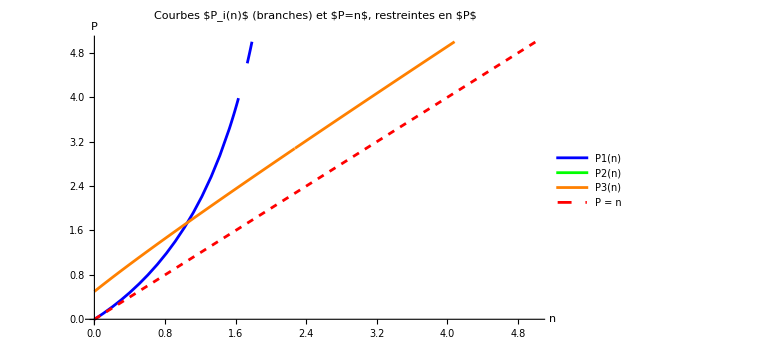

```mathematica
(*0) Nettoyage*)ClearAll[a,n,solutions,roots,F,Pfuns,kb,ka,mu,eta,lambdaa,lambdab];

(*1) Valeurs des constantes*)
kb=0.3;ka=0.7;
mu=0.2;eta=0.1;
lambdab=1.0;lambdaa=1.0;

(*2) Définition du polynôme g(a,n)*)
g[a_,n_]:=kb*mu*a^3+(mu+kb*eta)*a^2+(eta-lambdab-kb*n)*a-n;

(*3) Calcul symbolique des 3 racines*)
solutions=Solve[g[a,n]==0,a];
(*solutions est une liste de 3 règles {a->racine1},{a->racine2},{a->racine3}*)

(*4) Extraction des expressions des racines*)
roots=a/. solutions;
(*roots est une liste de trois expressions en fonction de n*)

(*5) Définition de F[a]*)
F[a_]:=(lambdab/(1+kb*a)-lambdaa/(1+ka*a))*a;

(*6) Construction de la liste des fonctions P_i(n)=n+F(racine_i(n))*)
Pfuns=(n+F[#]&/@roots);
(*Pfuns est une liste {P1[n],P2[n],P3[n]}*)

Plot[Evaluate[Join[Pfuns,{n}]],(*P1,P2,P3 et P=n*){n,0,5},(*domaine de n*)PlotStyle->{Blue,Green,Orange,{Red,Dashed}},PlotLegends->{"P1(n)","P2(n)","P3(n)","P = n"},AxesLabel->{"n","P"},PlotRange->{{0,5},{0,5}},(*[nmin,nmax]×[Pmin,Pmax]*)ImageSize->Large,PlotLabel->"Courbes $P_i(n)$ (branches) et $P=n$, restreintes en $P$"]
```